### Import packages

```mathematica
SetDirectory["/Users/koichiro/Downloads/FeynArts-3.12"];
<< FeynArts`
```

FeynArts 3.12 (24 May 2024)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
SetDirectory["/Users/koichiro/Downloads/FormCalc-9.10"];
```

```mathematica
<<FormCalc`
```

FormCalc 9.10 (16 Jan 2023)

by Thomas Hahn

$Aborted

### Generate processes

Excluding 1 Generic, 14 Classes, and 14 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

Restoring 1 Generic, 14 Classes, and 14 Particles fields

in total: 1 Classes insertion

> Top. 1 ad/bdcd/0.m, 0 diagrams

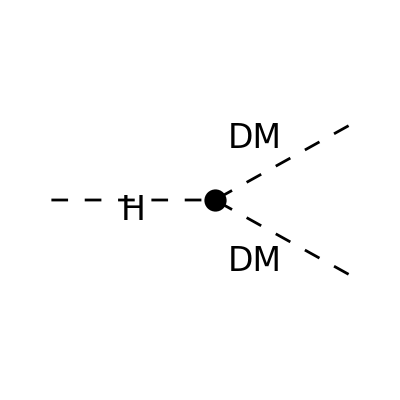

FeynArtsGraphics[][([])]

```mathematica
ins=InsertFields[
CreateTopologies[0,1->2,ExcludeTopologies->{}],{S[1]}->{S[99],S[99]},
GenericModel->"/Users/koichiro/Downloads/feynrules-samples/model2/Higgs-portal_FA/Higgs-portal_FA",Model->"/Users/koichiro/Downloads/feynrules-samples/model2/Higgs-portal_FA/Higgs-portal_FA",
InsertionLevel->{Classes},
ExcludeParticles->{V[1],V[2],V[3],U}];
Paint[ins,PaintLevel->{Classes},AutoEdit->False,SheetHeader->False,Numbering->False,ColumnsXRows->1]
```

### Feynman amplitude (squared)

```mathematica
amp =CalcFeynAmp[CreateFeynAmp[ins]];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

```mathematica
amp/.Amp[x_][y_]->y//.Subexpr[]//.Abbr[]/.M$FACouplings//Simplify
```

ReplaceRepeated::reps: {Subexpr[]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Abbr[]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

CalcFeynAmp[FeynAmpList[Process→{{S[1],p1,MH,{}}}→{{S[99],k1,Mdm,{}},{S[99],k2,Mdm,{}}},Model→{/Users/koichiro/Downloads/feynrules-samples/model2/Higgs-portal_FA/Higgs-portal_FA},GenericModel→{/Users/koichiro/Downloads/feynrules-samples/model2/Higgs-portal_FA/Higgs-portal_FA},AmplitudeLevel→{Classes},ExcludeParticles→{U,-U[1],U[1],-U[2],U[2],-U[4],U[4],-U[31],U[31],-U[32],U[32],-U[4,{_}],U[4,{_}],V[1],V[2],-V[3],V[3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Classes==1,Number==1],Integral[],cDM vev]]]//.Subexpr[]//.Abbr[]

```mathematica
M2=SquaredME[amp]//.Subexpr[]//.Abbr[]/.M$FACouplings;
```

ReplaceRepeated::reps: {Subexpr[]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Abbr[]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

### decay rate

```mathematica
info={βf->√(1-(4 Mdm^2)/MH2),dΦ->βf/(16π),MH->Mh,MH2->Mh^2};
```

```mathematica
$Assumptions={cDM>0,cDM∈Reals,vev>0,vev∈Reals};
```

#### total cross section: H→DM DM

```mathematica
ΓDM=Simplify[Integrate[1/2 1/(2MH)M2 dΦ//.info,{cosθ,-1,1}]]
```

ReplaceRepeated::reps: {Subexpr[]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Abbr[]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∫_-1^1 1/(64 Mh π)√(1-(4 Mdm^2)/Mh^2) (SquaredME[CalcFeynAmp[FeynAmpList[Process→{{S[1],p1,Mh,{}}}→{{S[99],k1,Mdm,{}},{S[99],k2,Mdm,{}}},Model→{/Users/koichiro/Downloads/feynrules-samples/model2/Higgs-portal_FA/Higgs-portal_FA},GenericModel→{/Users/koichiro/Downloads/feynrules-samples/model2/Higgs-portal_FA/Higgs-portal_FA},AmplitudeLevel→{Classes},ExcludeParticles→{U,-U[1],U[1],-U[2],U[2],-U[4],U[4],-U[31],U[31],-U[32],U[32],-U[4,{_}],U[4,{_}],V[1],V[2],-V[3],V[3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Classes==1,Number==1],Integral[],cDM vev]]]]//.Subexpr[]//.Abbr[])ⅆcosθ

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00